```mathematica
ClearAll[α,d,ωR,ωE,μ,θ,κ,βR,βE,τ,P,R1,R2,R3,Er,i,YR,imax,θan]
```

```mathematica
imax=8; μ=48; d=0.00025;(*sets parameters*) (*from 2008 paper*)
(*d = death rate of RBCs - what about bystander killing? Cromer et al. est. is 0.0095 for first six days of infection*)
(*parasite clearance p = 0.0095*)
βR=0.000274 (*0.00015*); (*invasion rates - normo rate from 2008 paper*)
βE=0.00000183;

ωR=9;ωE=9;(*Burst sizes for reticulocytes and normocytes, from July 2017 paper *)

θ=0.1; θan=0.52509; (*recovery coefficient for erythropoesis, from 2008 paper*)

τ=2; (*lag time for erythropoesis, from 2008 paper*)
κ=6000000; (*steady state RBC density, from Cromer paper*)
Table[R1[i]=κ*0.0033,{i,-100,0}]; (*sets retics to be 3%*)
Table[R2[i]=κ*0.0033,{i,-100,0}];
Table[R3[i]=κ*0.0033,{i,-100,0}];
Table[Er[i]=κ*0.99,{i,-100,0}];
Table[P[i]=0,{i,-100,-1}];
P[0] =855*9; (*10^5 infected RBCs, divided by 1170 μl per mouse, times 9 parasites per burst cell*)
IR[0]=0;
IEr[0]=0;
```

```mathematica
α=βR*(R1[i-1]+R2[i-1]+R3[i-1])+βE*Er[i-1]+μ;
YR=R1[i-1]+R2[i-1]+R3[i-1];
```

```mathematica
For[i =1,i< imax,i++,
If[R1[i-1]+R2[i-1]+R3[i-1]+Er[i-1]<(0.5*κ),theta=θan, theta=θ];
P[i]={(1-d) ((1-ⅇ^(-(βR P[-1+i])/α)) YR ωR+(1-ⅇ^(-(βE P[-1+i])/α)) ωE Er[-1+i])};
R1[i]=theta (κ-Er[-1+i]-R1[-1+i]-R2[-1+i]-R3[-1+i]);
R2[i]=(1-d) ⅇ^(-(βR P[-1+i])/α) R1[-1+i];
R3[i]=(1-d) ⅇ^(-(βR P[-1+i])/α) R2[-1+i];
Er[i]=(1-d) (ⅇ^(-(βE P[-1+i])/α) Er[-1+i]+ⅇ^(-(βR P[-1+i])/α) R3[-1+i]);
IR[i]=(1-ⅇ^(-(βR P[-1+i])/α))*YR*(1-d);
IEr[i]=(1-ⅇ^(-(βE P[-1+i])/α))*Er[-1+i];
];
ParaTab=Flatten[Table[P[i],{i,0,imax-1}]];
Retics=Flatten[Table[R1[i]+R2[i]+R3[i],{i,0,imax-1}]];
Normos=Flatten[Table[Er[i],{i,0,imax-1}]];
RBCtot=Retics+Normos;
ParaTabAdj=Flatten[Table[(Part[Retics,i]/Part[RBCtot,i])*βR+(Part[Normos,i]/Part[RBCtot,i])*βE, {i, 0, imax-1}]];
ParaTabRaw=Flatten[Table[(Part[Retics,i]/Part[RBCtot,i])*βE+(Part[Normos,i]/Part[RBCtot,i])*βE, {i, 0, imax-1}]];
IRTab=Flatten[Table[IR[i],{i,0,imax-1}]];
IErTab=Flatten[Table[IEr[i],{i,0,imax-1}]];
```

```mathematica
NaiveTot = 6000000;
AcuteTot = Part[RBCtot, 5];
NaiveRetic = NaiveTot*0.02;
AcuteRetic=Part[Retics,5];
DonorTotNav=(NaiveTot*0.031)/(0.969);
DonorTotAcu=(AcuteTot*0.036)/(0.964);
DonorReticAcu=DonorTotAcu*(Part[Retics,3]/Part[RBCtot,3]);
DonorReticNav=DonorTotNav*(Part[Retics,3]/Part[RBCtot,3]);
DonorPropAcu =DonorReticAcu/(DonorReticAcu+AcuteRetic);
DonorPropNav=DonorReticNav/(DonorReticNav+NaiveRetic);
DonorPropAcu/DonorPropNav (*first printed item below*)
DonorPropAcu 
DonorPropNav
```

31.1049

0.148742

0.00478194

```mathematica
Retics/RBCtot
```

{0.00990099,0.00643093,0.00300385,0.000289682,0.000641994,0.00113734,0.00184965,0.00305613}

```mathematica
NaiveTot = 6000000;
AcuteTot = Part[RBCtot, 5];
NaiveRetic = NaiveTot*0.01;
AcuteRetic=Part[Retics,5];
x=((Part[Retics,3]+Part[IRTab,3])/(Part[RBCtot,3]+Part[IErTab,3]+Part[IRTab,3])*0.031)/((0.01*0.969)+((Part[Retics,3]+Part[IRTab,3])/(Part[RBCtot,3]+Part[IErTab,3]+Part[IRTab,3])*0.031))
Part[Retics,5]/Part[RBCtot,5]
```

0.011384

0.000641994

IGNORE EVERYTHING BENEATH THIS (or risk seeing my questionable grasp of mathematics/science)

```mathematica
(Part[Retics,5]+Part[IRTab,5])/(Part[RBCtot,5]+Part[IRTab,5]+Part[IErTab,5])
```

0.000779699

```mathematica
(0.036*0.00867386)/0.32-0.036*0.00867386
```

0.00066355

```mathematica
0.00066355/0.964
```

0.00068833

```mathematica
0.00969/1.11715
```

0.00867386

What do I need?
1) Proportion uninfected cells that are retics
	At day 3: 0.00601215
	At day 5: 0.000802288
2) Proportion uninfected that are normos
	At day 3: 0.993988
	At day 5: 0.999198
3) Uninfected RBC total
	At day 3: 5.98 x 10^6
	At day 5: 5.92 x 10^6
4) Proportion total that are infected
	At day 3: 0.00169467
	At day 5: 0.00722626

{118800.,77372.9,35108.7,2192.22,5513.29,10398.2,18011.9,30668.9}

```mathematica
183093*0.0007347
```

134.518

Normocytes

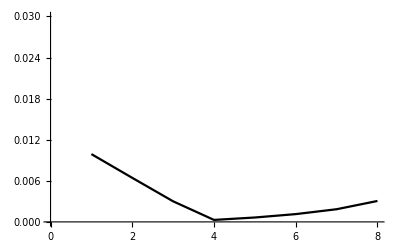

```mathematica
Print["Normocytes"]
ListPlot[{Retics/RBCtot}, Joined->True, PlotRange->{0,0.03},PlotStyle->{Black, Directive[Black, Dashing[0.01]]}] (*Data in dashed line*)
```

Number donor cells infected per microlitre (reticuloycte age preference)

```mathematica
(Part[Retics, 3]/Part[RBCtot,3]*βR+Part[Normos,3]/Part[RBCtot, 3]*βE)*0.036
```

1.24788×10^-7

Number recipient cells infected per microlitre (reticulocyte age preference)

```mathematica
(Part[Retics,5]/Part[RBCtot, 5]*βR+Part[Normos,5]/Part[RBCtot,5]*βE)*0.964
```

1.97462×10^-6

Number donor cells infected per microlitre (no age preference)

```mathematica
(Part[Retics, 3]/Part[RBCtot,3]*βE+Part[Normos,3]/Part[RBCtot, 3]*βE)*0.036
```

6.588×10^-8

Number recipient cells infected per microlitre (no age preference)

```mathematica
(Part[Retics,5]/Part[RBCtot, 5]*βE+Part[Normos,5]/Part[RBCtot,5]*βE)*0.964
```

1.76412×10^-6

Proportional increase in number cells infected without age preference

Donor cells

```mathematica
(0.748727-0.39528)/0.39528
```

0.894169

Recipient cells

```mathematica
(11.8477-10.5847)/10.5847
```

0.119323

```mathematica
{{(*# Cells infected per μL*), (*No age pref*), (*Retic pref*), (*% increase in inf. cell #*)}, {(*Donor, from day 3*), 0.39528, 0.748727, 89%}, {(*Recipient, from day 5*), 10.5847, 11.8477, 12%}}
```

```mathematica
IErTab/(RBCtot+IRTab+IErTab)
```

{0.,0.000156502,0.000725969,0.00282196,0.00770573,0.0128323,0.0212634,0.0340992}

```mathematica
((IRTab+IErTab)*5918549)/(RBCtot+IRTab+IErTab)
```

{0.,2860.66,10030.,25163.1,42769.,73216.6}

```mathematica
RBCtot
```

RBCtot

```mathematica
(*Recipient RBCs at day five infection*)
R=Part[RBCtot,5]+Part[IErTab,5]+Part[IRTab,5]
(*Donor RBCs transfused to make up 3.6% of total*)
Don=(R*0.036)/0.964
(*Recipient retics at transfusion*)
Part[Retics,5]/(Part[RBCtot, 5]+Part[IErTab,5]+Part[IRTab,5])*R
(*Donor retics at transfusion*)
Part[Retics,3]/(Part[RBCtot, 3]+Part[IRTab,3]+Part[IErTab,3])*Don
(*Recipient normos at transfusion*)
Part[Normos,5]/(Part[RBCtot, 5]+Part[IErTab,5]+Part[IRTab,5])*R
(*Donor normos at transfusion*)
(Part[IErTab,3]+Part[IRTab,3])/(Part[RBCtot, 3]+Part[IRTab,3]+Part[IErTab,3])*Don
```

5.97152×10^6

223003.

3868.27

667.45

5.93982×10^6

284.327

```mathematica
Part[IRTab,3]+Part[IErTab,3]
```

7642.46

```mathematica
Retics
```

{59400.,38554.7,17983.1,1729.55,3816.46,6712.3,10782.9,17454.2}

```mathematica
Part[Retics,1]
```

39650.1

```mathematica
R1[0]*3
```

180.

```mathematica
R1[3]
```

{1329.7}

```mathematica
R1[4]
```

{{2948.17}}